```mathematica
Clear["Global`*"]
```

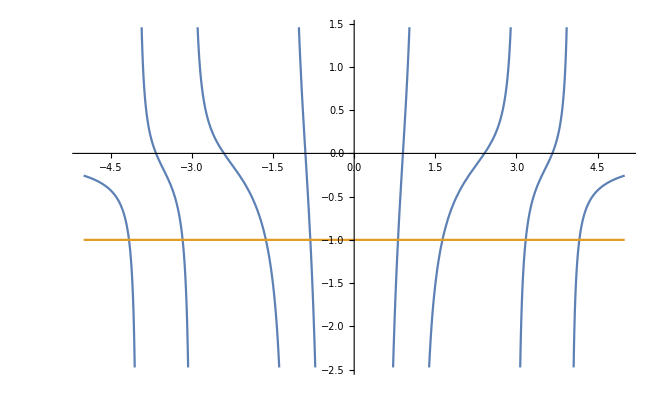

```mathematica
Plot[{1/(0.5^2-x^2)+1/(1.2^2-x^2)+1/(3^2-x^2)+1/(4^2-x^2),-1},{x,-5,5}]
```

```mathematica
poles[n_]:=Array[#&,n,{-5,5}]
```

```mathematica
chi[n_]:=Total[Exp[-Abs[#]]/(#^2-x^2)&/@poles[n]]
```

```mathematica
chi[5]
```

-1/x^2+2/(ⅇ^(5/2) (25/4-x^2))+2/(ⅇ^5 (25-x^2))

```mathematica
Manipulate[
Plot[Evaluate@{chi[n],-1},{x,-5,5}],{n,1,100,1}]
```

```mathematica
Limit[1/4*1/x(1-x^2)Log@Abs[(x+1)/(x-1)],x->0]
```

1/2

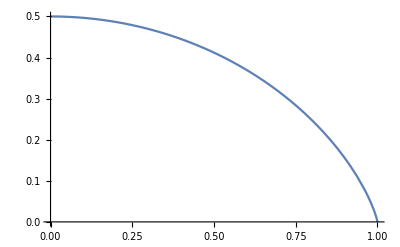

```mathematica
Plot[1/4*1/x(1-x^2)Log@Abs[(x+1)/(x-1)],{x,0,1}]
```